-Graphics-

Five Qubit Error Stabilizer Code
by Aditya Dhumuntarao

Quantum computers built with physical qubits are susceptible to propagation of error due to either decoherence, thermal, or other quantum noise thereby lowering the trust in the computational output. One clever (but computationally expensive) way around this is to devise special codes which not only produce high fidelity results even if a few errors accumulate but also have a clear syndrome which encodes the type of error that occurred and its location.

One such famous code is the five qubit error correcting code. In this code, five physical qubits are arranged in such a way that they encode a single logical qubit. Then any single qubit error, such as a bit or phase flip error, does not disturb (much) the information which is stored among the physical qubits. In this way, the five qubit error correcting code protects a single logical qubits from any single physical qubit error. Furthermore, there is a clear diagnostic, namely the syndrome, which can be extracted from the code and used to determine what the error type is and where the error occurred in order to correct it.

In this short notebook, I show how to construct the [[5,1,3]] stabilizer code in Mathematica.

## [[5,1,3]] Code Construction

```mathematica
PacletInstall[CloudObject["https://wolfr.am/DevWQCF"],ForceVersionInstall->True]
<< Wolfram`QuantumFramework`
```

PacletObject[…]

If  are the two Pauli matrices and the identity matrix respectively, then the generators for the code are given by cyclic permutations of the following stabilizer

```mathematica
S1={X,Z,Z,X,Identity}
```

{X,Z,Z,X,Identity}

The cyclic permutations are given by

```mathematica
Stabilizers=Table[RotateRight[S1,i],{i,0,Length[S1]-2}]
```

{{X,Z,Z,X,Identity},{Identity,X,Z,Z,X},{X,Identity,X,Z,Z},{Z,X,Identity,X,Z}}

Now, we have to introduce these gates at the appropriate site location within the logical qubit. The site locations can be given by

```mathematica
Sites=Partition[SortBy[Flatten[Table[{i,4+j},{i,1,4},{j,1,5}],1],Total],5]
```

{{{1,5},{1,6},{2,5},{1,7},{2,6}},{{3,5},{1,8},{2,7},{3,6},{4,5}},{{1,9},{2,8},{3,7},{4,6},{2,9}},{{3,8},{4,7},{3,9},{4,8},{4,9}}}

Lastly, we can design the circuit. We do this as follows. The top four registers are acted upon a Hadamard. Then the full set of stabilizers are encoded into the register corresponding to the logical qubit at the site locations described above. The last step is to again act on the ancillas with Hadamards and then measure to see if any errors have occurred. The circuit is shown below!

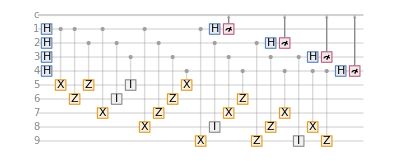

```mathematica
QECC5=Flatten[Join[Table[QuantumOperator["Hadamard",{i}],{i,4}],Table[Table[(QuantumOperator[{"Controlled",ToString[Stabilizers[[j,i]]]},Sites[[j,i]]]),{i,Length[Stabilizers[[1]]]}],{j,Length[Sites]}],Table[QuantumOperator["Hadamard",{i}],{i,4}],Table[QuantumMeasurementOperator[{i}],{i,4}]]];
Show[QuantumCircuitOperator[QECC5]["Diagram"],ImageSize->Full]
```